```mathematica
Pollaczek-Khinchine transform equation
```

Pollaczek-equation Khinchine transform

```mathematica
Clear["Global`*"]
```

```mathematica
Γ=GammaDistribution[α,β] 
𝒫=PDF[Γ,x]
Mean[Γ]
```

GammaDistribution[α,β]

Piecewise[{{(ⅇ^(-x/β) x^(-1+α) β^-α)/Gamma[α], x>0}, {0, True}}]

α β

```mathematica
Manipulate[Plot[PDF[GammaDistribution[α,β],x],{x,0,5},Filling->Axis],
{{α,2},0,5},{{β,1},0.1,1}]
```

```mathematica
Sojourn time transform
```

Sojourn time transform

```mathematica
g[s_]:=Evaluate[LaplaceTransform[𝒫,x,s]]
Information[g]
```

Global`g

g[s_]:=(s+1/β)^-α β^-α

```mathematica
ClearAll[W]
W[s_,λ_,μ_,g_]:=Module[{ρ=λ/μ},((1-ρ)s g[s])/(s-λ(1-g[s]))]
Information[W]
```

Global`W

W[s_,λ_,μ_,g_]:=Module[{ρ=λ/μ},((1-ρ) s g[s])/(s-λ (1-g[s]))]

```mathematica
ℰ=ExponentialDistribution[μ]
g[s_]:=Evaluate[LaplaceTransform[PDF[ℰ,x],x,s]]
Information[g]
wL=W[s,λ,1/Mean[ℰ],g]
w=Simplify[InverseLaplaceTransform[wL,s,x]]
```

ExponentialDistribution[μ]

Global`g

g[s_]:=μ/(s+μ)

(s (1-λ/μ) μ)/((s+μ) (s-λ (1-μ/(s+μ))))

ⅇ^(x (λ-μ)) (-λ+μ)

```mathematica
Γ=GammaDistribution[α,β] 
𝒫=PDF[Γ,x]
g[s_]:=Evaluate[LaplaceTransform[𝒫,x,s]]
Information[g]
wL=W[s,λ,1/Mean[Γ],g]
Assuming[{α∈Reals,β∈Reals,λ∈Reals,x∈Reals,x>0,λ<α β},InverseLaplaceTransform[wL,s,x]]
```

GammaDistribution[α,β]

Piecewise[{{(ⅇ^(-x/β) x^(-1+α) β^-α)/Gamma[α], x>0}, {0, True}}]

Global`g

g[s_]:=(s+1/β)^-α β^-α

(s (s+1/β)^-α β^-α (1-α β λ))/(s-(1-(s+1/β)^-α β^-α) λ)

β^-α (1-α β λ) InverseLaplaceTransform[(s (s+1/β)^-α)/(s-(1-(s+1/β)^-α β^-α) λ),s,x]

```mathematica
<<"~/Desktop/NumericalInversion.m"
```

f::shdw: Symbol "f" appears in multiple contexts {"NumericalMath`NumericalInversion`", "Global`"}; definitions in context "NumericalMath`NumericalInversion`" may shadow or be shadowed by other definitions.

```mathematica
?Durbin
```

Finds numerically the inverse f(t) of F(s) 

The command is Durbin[ F(s),s,t,N,α,ϵ] 

Defaults are N = 1000, α = 0, ϵ = 2

s/(50 (1+s)^2 (s-49/100 (1-1/(1+s)^2)))

-(2 (ⅇ^((-151/200-(7 √449)/200) x)-ⅇ^((-151/200+(7 √449)/200) x)))/(7 √449)

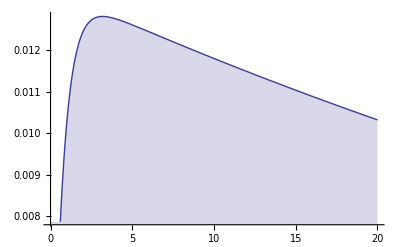

```mathematica
fL=wL/.{α->2,β->1,λ->1/2-1/100}
f=InverseLaplaceTransform[fL,s,x]
Plot[f,{x,0,20},Filling->Axis]
```

```mathematica
Clear[g]
Γ=GammaDistribution[α,β] 
𝒫=PDF[Γ,x]
L[s_]:=Evaluate[LaplaceTransform[𝒫,x,s]]
Information[L]
```

GammaDistribution[α,β]

Piecewise[{{(ⅇ^(-x/β) x^(-1+α) β^-α)/Gamma[α], x>0}, {0, True}}]

Global`L

L[s_]:=(s+1/β)^-α β^-α

```mathematica
(W[s,λ,μ,g]/.`g[s]->g)==L
Solve[%,g]
```

(g s (1-λ/μ))/(s-(1-g) λ)==L

{{g→(-L s μ+L λ μ)/(s λ-s μ+L λ μ)}}

```mathematica
pi[z_,g_]:=((1-z)(1-ρ)g[λ(1-z)])/(g[λ(1-z)]-z)
w[z_,g_]:=((1-ρ)z g[z])/(z-λ(1-g[z]))
solution=Simplify[Solve[w[z]==w[z,g],g[z]]]
```